```mathematica
(* The Base directory when working on the lab computer *)
labComp=FileNameJoin[{"C:","Users","karl","Dropbox","00School","gradYear03Spring","research"}];
(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{labComp,"2-17-17_plusMinus"}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",Infinity],DirectoryQ];
For[i=1,i<=Length[directories],i++,
Print[i -> directories[[i]]];]
```

C:\Users\karl\Dropbox\00School\gradYear03Spring\research\2-17-17_plusMinus

1→img

2→negativeDetunings

3→positiveDetunings

{FDayScan2017-02-17_185952RotationAnalysis.dat,FDayScan2017-02-17_190154RotationAnalysis.dat,FDayScan2017-02-17_190356RotationAnalysis.dat}

RbAbs2017-02-17_185715.dat

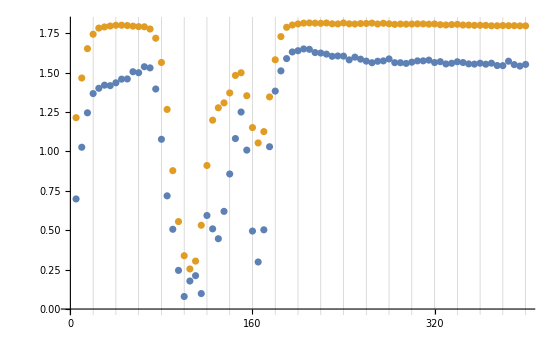

Import::nffil: File not found during Import.

```mathematica
(* set rootFolder to the folder name containing the RbPolarization Files *)
rootFolder=FileNameJoin[{dataFolder,directories[[2]]}];
SetDirectory[rootFolder];
(* Obtain the filename of the absorption data *)
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"]
noPump=scanFiles[[1]];

(*** In the future, the following will be removed as we will no longer take an absorption
profile in order to calculate the detunings. ***) 
absFileName=FileNames["RbAbs*.dat"][[1]]
(*Import the faraday rotation data*)
rotationAnalysisDataFile=Import[FileNameJoin[{rootFolder,scanFiles[[1]]}],"tsv"];
(*Import the absorption data*)
rbAbsorption=Import[FileNameJoin[{Directory[],absFileName}],"tsv"];
(* Drop the information from the file that isn't needed *)
rbAbsorptionRef=Drop[Take[rbAbsorption,{8,-2},{1,6}],None,{2,5}];
rbAbsorptionPro=Drop[Take[rbAbsorption,{8,-2},{1,4}],None,{2,3}];
(* Plot the data so the user can see the first minimum *)
ListPlot[{rbAbsorptionPro,rbAbsorptionRef},Ticks-> {Range[0,1023,20],Automatic},GridLines->{Range[0,1023,20],None}]

(*** Instead, it will be replaced with this code, which reads in a .tsv with the detunings used. ***)
detuningRun1=Transpose[Import["firstRunDetunings.tsv","tsv"]][[1]];
```

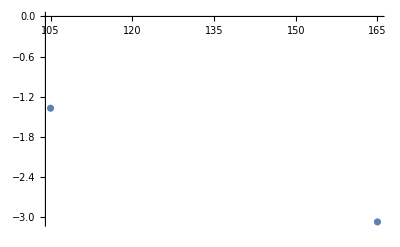

105.52-0.394071 x+0.759312 x^2

2.98806

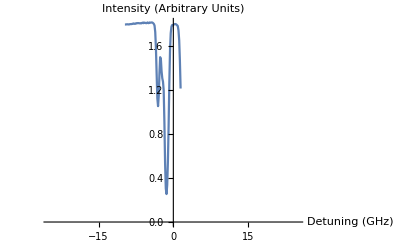

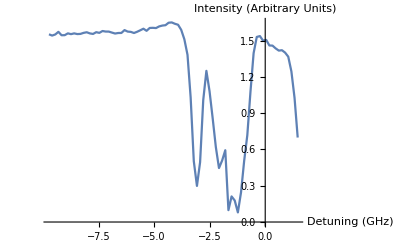

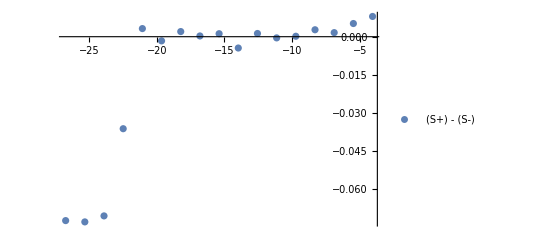

-Graphics-

```mathematica
(* User inputs a value close to the first minimum *)
{transistionLetter,aoutValue}={"B",100};
CtoDDiff=110;
BtoCDiff=135;
AtoBDiff=72;
dt=4.576;
ct=1.84;
bt=-1.372;
at=-3.072;
transGHz={4.576,1.84,-1.372,-3.072};
aoutSteps={CtoDDiff,BtoCDiff,AtoBDiff};


(* Find the closest data point to the value chosen by the user*)
s=Nearest[Take[rbAbsorptionRef,All,1],aoutValue];
(* Convert this data point to a position in the list *)
startPos=Position[Take[rbAbsorptionRef,All,1],s[[1]]][[1]][[1]];
(* Use the position in the list to find the first absorption peak's value *)
scanStepSize=(rbAbsorptionRef[[startPos]]-rbAbsorptionRef[[startPos+1]])[[1]];
posLower=startPos-3;
posUpper=startPos+1;
transAout={0,0,0,0};
i=0;

If[transistionLetter=="D",j=1,If[transistionLetter=="C",j=2,If[transistionLetter=="B",j=3,If[transistionLetter=="A",j=4,j=5]]]];
(* Cycle through and find the remaining transisition "peaks" *)
While[And[posLower>1,j<5],
peak=Min[Take[rbAbsorptionRef,{posLower,posUpper},All]];
(* Use the value of the first absorption peak to find its position in the list *)
aoutPos=Position[rbAbsorptionRef,peak][[1]][[1]];
(* Use the position in the list to get the Aout value located there *)
transAout[[j]]=rbAbsorptionRef[[aoutPos]][[1]];
(* Because the profile is consistent, we can guess at where the next min. will be*)
If[j<4,aoutPrev=transAout[[j]];aoutStep=aoutSteps[[j]];aoutNextApprox=aoutPrev+aoutStep;
s=Nearest[Take[rbAbsorptionRef,All,1],aoutNextApprox];
posLower=aoutPos-Floor[aoutStep/scanStepSize]-1*Floor[20/scanStepSize];
posUpper=aoutPos-Floor[aoutStep/scanStepSize]+1*Floor[20/scanStepSize];
];
j++;
]
(* Remove the transistions that we don't have from the list so that we can estimate a linear 
function relating the data points that we do have *)
aoutConvData=Dataset[Transpose[{transAout,transGHz}]];
aoutConvData=aoutConvData[Select[Abs[#[[1]]]>0&]];
aoutConvData=Normal[aoutConvData];

(* Make a linear fit on the data to obtain an AOUT->GHz Conversion *)
ListPlot[aoutConvData]
lm2=LinearModelFit[aoutConvData,x,x];
aoutConv=lm2["BestFitParameters"][[2]];
aoutIntercept=lm2["BestFitParameters"][[1]];
rotationAnalysisData=rotationAnalysisDataFile;

(* Retrieves the recorded voltages of the magnets *)
v1=rotationAnalysisData[[11]][[2]];
v2=rotationAnalysisData[[12]][[2]];
(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1=v1*c1v2iSlope+c1v2iInt;
i2=v2*c2v2iSlope+c2v2iInt;

(*Creates a function for obtaining the magnetic field at a given position based on the currents
in the magnets *)
getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2)  ;
getBEq[i1,i2]
BdotL=Integrate[getBEq[i1,i2],{x,0,2.794}] /100;(* Divide by 100 to convert to Tesla*meters*)

{aoutAbs,iPro}=Transpose[rbAbsorptionPro];
{aoutAbs,iRef}=Transpose[rbAbsorptionRef];
{detuneAbs,iPro}={aoutAbs*aoutConv+aoutIntercept,iPro};
{detuneAbs,iRef}={detuneAbs,iRef};
rbAbsPro=Transpose[{detuneAbs,iPro}];
rbAbsRef=Transpose[{detuneAbs,iRef}];
ListPlot[{rbAbsRef},PlotRange-> {{-25,25},Automatic},Joined->True,AxesLabel->{"Detuning (GHz)","Intensity (Arbitrary Units)"},LabelStyle->14]
ListPlot[{rbAbsPro},PlotRange-> {All,All},Joined->True,AxesLabel->{"Detuning (GHz)","Intensity (Arbitrary Units)"},LabelStyle->14]

rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[1]]}],"tsv"];
rotationAnalysisData=Drop[Take[rotationAnalysisData,{14,-1},{1,9}],None,{2,8}];
{aout,θDeg}=Transpose[rotationAnalysisData];
{detune,θRad}={aout*aoutConv+aoutIntercept,θDeg*Pi/180};
rotationAnalysisData =Transpose[{detune,θRad}];
noPump=rotationAnalysisData;
rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[2]]}],"tsv"];
rotationAnalysisData=Drop[Take[rotationAnalysisData,{14,-1},{1,9}],None,{2,8}];
{aout,θDeg}=Transpose[rotationAnalysisData];
{detune,θRad}={aout*aoutConv+aoutIntercept,θDeg*Pi/180};
rotationAnalysisData =Transpose[{detune,θRad}];
sPlusPump=rotationAnalysisData;
rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[3]]}],"tsv"];
rotationAnalysisData=Drop[Take[rotationAnalysisData,{14,-1},{1,9}],None,{2,8}];
{aout,θDeg}=Transpose[rotationAnalysisData];
{detune,θRad}={aout*aoutConv+aoutIntercept,θDeg*Pi/180};
rotationAnalysisData =Transpose[{detune,θRad}];
sMinusPump=rotationAnalysisData;
{detune,θm}=Transpose[sMinusPump];
{detune,θp}=Transpose[sPlusPump];
pumpDifference=Transpose[{detune,θp-θm}];
ListPlot[Legended[pumpDifference,"(S+) - (S-)"],PlotRange->All]
Rasterize[ListPlot[{Legended[noPump,"No Pump"],Legended[sPlusPump,"S+ Pump"],Legended[sMinusPump,"S- Pump"]},PlotRange->All,LabelStyle->14,AxesLabel->{"Detuning (GHz)","Probe Laser\nPlane of Polarization"},ImageSize->Large]]
```

{{20.0094,-1.07642},{18.798,-1.07829},{17.5865,-1.07533},{16.3751,-1.07869},{15.1636,-1.07593},{13.9522,-1.07252},{12.7407,-1.06972},{11.5293,-1.07383},{10.3178,-1.07033},{9.10638,-1.06551},{7.89494,-1.06536},{6.68349,-1.05944},{5.47204,-1.04869}}

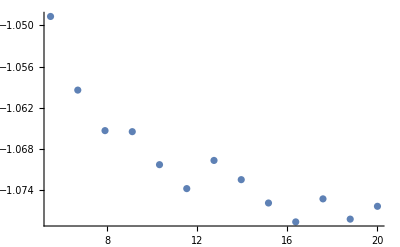

```mathematica
posDetunings = noPump
ListPlot[posDetunings]
```

```mathematica
negDetunings=noPump
```

{{-4.06367,-0.775462},{-5.48033,-0.987604},{-6.897,-1.02803},{-8.31367,-1.04741},{-9.73033,-1.05487},{-11.147,-1.06016},{-12.5637,-1.06622},{-13.9803,-1.06818},{-15.397,-1.07104},{-16.8137,-1.07089},{-18.2303,-1.07262},{-19.647,-1.07417},{-21.0637,-1.07913},{-22.4803,-1.07645},{-23.897,-1.07651},{-25.3137,-1.07798},{-26.7303,-1.0781}}

```mathematica
everything=Join[posDetunings,negDetunings]
```

{{20.0094,-1.07642},{18.798,-1.07829},{17.5865,-1.07533},{16.3751,-1.07869},{15.1636,-1.07593},{13.9522,-1.07252},{12.7407,-1.06972},{11.5293,-1.07383},{10.3178,-1.07033},{9.10638,-1.06551},{7.89494,-1.06536},{6.68349,-1.05944},{5.47204,-1.04869},{-4.06367,-0.775462},{-5.48033,-0.987604},{-6.897,-1.02803},{-8.31367,-1.04741},{-9.73033,-1.05487},{-11.147,-1.06016},{-12.5637,-1.06622},{-13.9803,-1.06818},{-15.397,-1.07104},{-16.8137,-1.07089},{-18.2303,-1.07262},{-19.647,-1.07417},{-21.0637,-1.07913},{-22.4803,-1.07645},{-23.897,-1.07651},{-25.3137,-1.07798},{-26.7303,-1.0781}}

```mathematica
(* Calculates fit for data *)
(* Removes datapoints that wrapped in rotation *)
lowerBoundDetuning=5;
upperBoundDetuning= 20;
dataset=Dataset[everything];
dataset=dataset[Select[Abs[#[[1]]]<upperBoundDetuning&]];
dataset=dataset[Select[Abs[#[[1]]]>lowerBoundDetuning&]];
alldata = Normal[dataset];
lowerBoundDetuning=lowerBoundDetuning;
upperBoundDetuning= upperBoundDetuning;
pumpDiff=Dataset[pumpDifference];
pumpDiff=pumpDiff[Select[Abs[#[[1]]]<upperBoundDetuning&]];
pumpDiff=pumpDiff[Select[Abs[#[[1]]]>lowerBoundDetuning&]];
pumpDiff=Normal[pumpDiff];
labelSize=18;
color=Blue;
color2=LightOrange;

Clear[a,b,c,d,e]
$Assumptions=a>0;
$Assumptions=b>0;
dataset=Dataset[alldata];
maxmin=dataset[MinMax,2];
ListPlot[Normal[dataset],PlotRange->All]
νo=377.107;
(*maxmin={datasetmm[-1][2],datasetmm[1][2]};*)
model=a/(δ-e)^2+b/(δ-e)^4+d;
Print["Fit Parameters for Number Density"]
nlmFit =NonlinearModelFit[Normal[dataset],model(*,e>-10,e<10}*),{{a,1},{b,1},{d,0},{e,1}},δ];
replacements=nlmFit["BestFitParameters"]
plot=Plot[Legended[Evaluate[model/.replacements],"A_1/(δ - B)^2+A_2/(δ - B)^4+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->color,LabelStyle->labelSize];
modelf=Function[{δ},Evaluate[model/.replacements]];
Print["Parameter Errors 1/δ^2+1/δ^4"]
errors=nlmFit["ParameterErrors"]
errorList={(a/.replacements) +errors[[1]],(b/.replacements)+errors[[2]],(d/.replacements)+errors[[3]],(e/.replacements)+errors[[4]]}
plotPlusError=Plot[errorList[[1]]/(δ)^2+errorList[[2]]/(δ)^4+errorList[[3]],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->color2,LabelStyle->labelSize];
errorList={(a/.replacements) -errors[[1]],(b/.replacements)-errors[[2]],(d/.replacements)-errors[[3]],(e/.replacements)-errors[[4]]}
plotMinusError=Plot[Legended[errorList[[1]]/(δ)^2+errorList[[2]]/(δ)^4+errorList[[3]],"A_1/(δ - B)^2+A_2/(δ - B)^4+θ_o (Error)"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->color2,LabelStyle->labelSize];
{δl,θl}=Transpose[Normal[dataset]];
Print["Range of angles (rad)"];
range=Max[maxmin]-Min[maxmin];
θl;
Map[modelf,δl];
residuals=θl - Map[modelf,δl];
Print["Sum of Square of Residuals"];
residuals^2;


modelNo4=a/(δ-e)^2+d;
Print["Replacements Excluding δ^4"]
nlmFit2=NonlinearModelFit[Normal[dataset],modelNo4,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal->5];
replacementsNo4=nlmFit2["BestFitParameters"]
plotNo4=Plot[Legended[Evaluate[modelNo4/.replacementsNo4],"A_1/(δ - B)^2+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->Red,LabelStyle->labelSize];
modelfNo4=Function[{δ},Evaluate[modelNo4/.replacementsNo4]];
{δl,θl}=Transpose[Normal[dataset]];
Print["Parameter Errors 1/δ^2"]
errorsNo4=nlmFit2["ParameterErrors"]
errorList={(a/.replacements) +errorsNo4[[1]],(d/.replacements)+errorsNo4[[2]],(e/.replacements) +errorsNo4[[3]]}
plotNo4PlusError=Plot[errorList[[1]]/(δ-errorList[[3]])^2+errorList[[2]],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->LightRed,LabelStyle->labelSize];
errorList={(a/.replacements) -errorsNo4[[1]],(d/.replacements)-errorsNo4[[2]],(e/.replacements) -errorsNo4[[3]]}
plotNo4MinusError=Plot[Legended[errorList[[1]]/(δ-errorList[[3]])^2+errorList[[2]],"A_1/(δ - B)^2+θ_o (Error)"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->LightRed,LabelStyle->labelSize];


linearRotationFit=LinearModelFit[Normal[dataset],x,x];


(* Calculates fit for polarization *)
{detune,δθ}=Transpose[pumpDiff];
newThing=Transpose[{1/detune,δθ}];
lm=LinearModelFit[newThing,x,x]
polPlot=Plot[lm[x],{x,0,-.15}];
Show[{ListPlot[newThing],polPlot},PlotRange->All,AxesLabel->{"1/Detuning\n(GHz^-1)","θ_(S+)-θ_(S-)"},LabelStyle->14,ImageSize->Large]
slope=lm["BestFitParameters"][[2]];

Cpar=1.2692*^-11;
c=2.99792458*^8;
re=2.8179*^-15;
fge=0.34231;
k=4/3;
Print["Integrated Magnetic Field (T*m):"]
BdotL
μ=9.2740*^-24;
h=6.6261*^-34;
ν0=377107.463;
conversionFactor=h/(BdotL*c*re*fge*k*μ)*10^18*10^-6;(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)
Print["Number Density (cm^-3):"]
n=1*^13
errors=nlmFit["ParameterErrors"];
Print["Number Density Error (cm^-3):"]
nErr=errors[[1]]*conversionFactor
Print["Number Density Simple(cm^-3):"]
nNo4 =(a/.replacementsNo4)*conversionFactor
Print["Polarization:"]
pol=slope/(Cpar*n*2)
finalResult=Show[plot,plotNo4,ListPlot[Legended[everything,"Data Points"],LabelStyle->labelSize],AxesLabel->{"Detuning\n(GHz)","Plane of Polarization (rad)"},ImageSize->Large]
Rasterize[finalResult]
fitList={{"theta_0","A_1","B","theta_0'","A_1'","B'","A_2'"},
{d/.replacementsNo4,a/.replacementsNo4,e/.replacementsNo4,d/.replacements,a/.replacements,e/.replacements,b/.replacements},
{errorsNo4[[2]],errorsNo4[[1]],errorsNo4[[3]],errors[[3]],errors[[1]],errors[[4]],errors[[2]]}}
Export["fitStatistics.tsv",fitList]
```

ListPlot::lpn: … is not a list of numbers or pairs of numbers.

ListPlot[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],PlotRange→All]

Fit Parameters for Number Density

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]

General::prng: Value of option PlotRange -> … is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: -29.9988 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -29.9988 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Parameter Errors 1/δ^2+1/δ^4

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][ParameterErrors]

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

Part::partw: Part 4 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{ParameterErrors+(a/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]),NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][ParameterErrors]⟦2⟧+(b/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]),NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][ParameterErrors]⟦3⟧+(d/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]),NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][ParameterErrors]⟦4⟧+(e/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters])}

General::prng: Value of option PlotRange -> … is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: -29.9988 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -29.9988 is not a valid variable.

Part::partw: Part 2 of … does not exist.

General::ivar: -29.9988 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 4 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

Part::partw: Part 4 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{-ParameterErrors+(a/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]),-NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][ParameterErrors]⟦2⟧+(b/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]),-NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][ParameterErrors]⟦3⟧+(d/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]),-NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][ParameterErrors]⟦4⟧+(e/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters])}

General::prng: Value of option PlotRange -> … is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: -29.9988 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -29.9988 is not a valid variable.

Part::partw: Part 2 of … does not exist.

General::ivar: -29.9988 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 4 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::shape: Lists {δl,θl} and … are not the same shape.

Range of angles (rad)

General::ivar: 25.4157 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -25.3888 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -26.9066 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 25.4157 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -25.3888 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -26.9066 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Sum of Square of Residuals

General::ivar: 25.4157 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -25.3888 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -26.9066 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Replacements Excluding δ^4

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][BestFitParameters]

General::prng: Value of option PlotRange -> … is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: -29.9988 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -29.9988 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {δl,θl} and … are not the same shape.

Parameter Errors 1/δ^2

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][ParameterErrors]

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

Part::partw: Part 2 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{ParameterErrors+(a/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]),NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][ParameterErrors]⟦2⟧+(d/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]),NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][ParameterErrors]⟦3⟧+(e/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters])}

General::prng: Value of option PlotRange -> … is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: -29.9988 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -29.9988 is not a valid variable.

Part::partw: Part 2 of … does not exist.

General::ivar: -29.9988 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

Part::partw: Part 2 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{-ParameterErrors+(a/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]),-NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][ParameterErrors]⟦2⟧+(d/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]),-NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][ParameterErrors]⟦3⟧+(e/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters])}

General::prng: Value of option PlotRange -> … is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ivar: -29.9988 is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: -29.9988 is not a valid variable.

Part::partw: Part 2 of … does not exist.

General::ivar: -29.9988 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Set::shape: Lists {detune,δθ} and … are not the same shape.

Transpose::nmtx: The first two levels of {{1/(7.95005×10^6 aoutConv+aoutIntercept),1/(7.95007×10^6 aoutConv+aoutIntercept),1/(7.95009×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95014×10^6 aoutConv+aoutIntercept),1/(7.95016×10^6 aoutConv+aoutIntercept),1/(7.95019×10^6 aoutConv+aoutIntercept),1/(7.95021×10^6 aoutConv+aoutIntercept),1/(7.95024×10^6 «8»+«13»),1/(«1»+«13»),1/(«1»),1/(«1»),1/(«1»),1/(7.95038×10^6 aoutConv+«13»),1/(7.95041×10^6 aoutConv+aoutIntercept),1/(7.95044×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95053×10^6 aoutConv+aoutIntercept),1/(7.95056×10^6 aoutConv+aoutIntercept),1/(7.9506×10^6 aoutConv+aoutIntercept)},δθ} cannot be transposed.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Transpose[{{1/(7.95005×10^6 aoutConv+aoutIntercept),1/(7.95007×10^6 aoutConv+aoutIntercept),1/(7.95009×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95014×10^6 aoutConv+aoutIntercept),1/(7.95016×10^6 aoutConv+aoutIntercept),1/(7.95019×10^6 aoutConv+aoutIntercept),1/(7.95021×10^6 aoutConv+aoutIntercept),1/(7.95024×10^6 aoutConv+aoutIntercept),1/(7.95027×10^6 aoutConv+aoutIntercept),1/(7.95029×10^6 aoutConv+aoutIntercept),1/(7.95032×10^6 aoutConv+aoutIntercept),1/(7.95035×10^6 aoutConv+aoutIntercept),1/(7.95038×10^6 aoutConv+aoutIntercept),1/(7.95041×10^6 aoutConv+aoutIntercept),1/(7.95044×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95053×10^6 aoutConv+aoutIntercept),1/(7.95056×10^6 aoutConv+aoutIntercept),1/(7.9506×10^6 aoutConv+aoutIntercept)},δθ}],x,x]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{1/(7.95005×10^6 aoutConv+aoutIntercept),1/(7.95007×10^6 aoutConv+aoutIntercept),1/(7.95009×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95014×10^6 aoutConv+aoutIntercept),1/(7.95016×10^6 aoutConv+aoutIntercept),1/(7.95019×10^6 aoutConv+aoutIntercept),1/(7.95021×10^6 aoutConv+aoutIntercept),1/(«12» «8»+«13»),1/(«1»),1/(«1»),1/(«1»),1/(«1»+«13»),1/(7.95038×10^6 aoutConv+«13»),1/(7.95041×10^6 aoutConv+aoutIntercept),1/(7.95044×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95053×10^6 aoutConv+aoutIntercept),1/(7.95056×10^6 aoutConv+aoutIntercept),1/(7.9506×10^6 aoutConv+aoutIntercept)},δθ}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Show[{ListPlot[Transpose[{{1/(7.95005×10^6 aoutConv+aoutIntercept),1/(7.95007×10^6 aoutConv+aoutIntercept),1/(7.95009×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95014×10^6 aoutConv+aoutIntercept),1/(7.95016×10^6 aoutConv+aoutIntercept),1/(7.95019×10^6 aoutConv+aoutIntercept),1/(7.95021×10^6 aoutConv+aoutIntercept),1/(7.95024×10^6 aoutConv+aoutIntercept),1/(7.95027×10^6 aoutConv+aoutIntercept),1/(7.95029×10^6 aoutConv+aoutIntercept),1/(7.95032×10^6 aoutConv+aoutIntercept),1/(7.95035×10^6 aoutConv+aoutIntercept),1/(7.95038×10^6 aoutConv+aoutIntercept),1/(7.95041×10^6 aoutConv+aoutIntercept),1/(7.95044×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95053×10^6 aoutConv+aoutIntercept),1/(7.95056×10^6 aoutConv+aoutIntercept),1/(7.9506×10^6 aoutConv+aoutIntercept)},δθ}]],-Graphics-},PlotRange→All,AxesLabel→{1/Detuning
(GHz^-1),θ_(S+)-θ_(S-)},LabelStyle→14,ImageSize→Large]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partw: Part 2 of LinearModelFit[Transpose[{{1/(7.95005×10^6 aoutConv+aoutIntercept),1/(7.95007×10^6 aoutConv+aoutIntercept),1/(7.95009×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95014×10^6 aoutConv+aoutIntercept),1/(7.95016×10^6 aoutConv+aoutIntercept),1/(7.95019×10^6 aoutConv+aoutIntercept),1/(7.95021×10^6 aoutConv+aoutIntercept),«6»,1/(7.95041×10^6 aoutConv+aoutIntercept),1/(7.95044×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95053×10^6 aoutConv+aoutIntercept),1/(7.95056×10^6 aoutConv+aoutIntercept),1/(7.9506×10^6 aoutConv+aoutIntercept)},δθ}],x,x][BestFitParameters] does not exist.

Integrated Magnetic Field (T*m):

0.000298806

Number Density (cm^-3):

1213

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

Number Density Error (cm^-3):

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

6.20151×10^11 ParameterErrors

Number Density Simple(cm^-3):

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

6.20151×10^11 (a/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][BestFitParameters])

Polarization:

3.24772×10^7 LinearModelFit[Transpose[{{1/(7.95005×10^6 aoutConv+aoutIntercept),1/(7.95007×10^6 aoutConv+aoutIntercept),1/(7.95009×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95014×10^6 aoutConv+aoutIntercept),1/(7.95016×10^6 aoutConv+aoutIntercept),1/(7.95019×10^6 aoutConv+aoutIntercept),1/(7.95021×10^6 aoutConv+aoutIntercept),1/(7.95024×10^6 aoutConv+aoutIntercept),1/(7.95027×10^6 aoutConv+aoutIntercept),1/(7.95029×10^6 aoutConv+aoutIntercept),1/(7.95032×10^6 aoutConv+aoutIntercept),1/(7.95035×10^6 aoutConv+aoutIntercept),1/(7.95038×10^6 aoutConv+aoutIntercept),1/(7.95041×10^6 aoutConv+aoutIntercept),1/(7.95044×10^6 aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(-1. aoutConv+aoutIntercept),1/(7.95053×10^6 aoutConv+aoutIntercept),1/(7.95056×10^6 aoutConv+aoutIntercept),1/(7.9506×10^6 aoutConv+aoutIntercept)},δθ}],x,x][BestFitParameters]⟦2⟧

ListPlot::lpn: everything is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,-Graphics-,ListPlot[everything,LabelStyle→18],AxesLabel→{Detuning
(GHz),Plane of Polarization (rad)},ImageSize→Large]

-Graphics-

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of … does not exist.

Part::partw: Part 3 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{theta_0,A_1,B,theta_0',A_1',B',A_2'},{d/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][BestFitParameters],a/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][BestFitParameters],e/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][BestFitParameters],d/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters],a/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters],e/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters],b/.NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][BestFitParameters]},{NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][ParameterErrors]⟦2⟧,ParameterErrors,NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+a/(-e+δ)^2,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal→5][ParameterErrors]⟦3⟧,NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][ParameterErrors]⟦3⟧,ParameterErrors,NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][ParameterErrors]⟦4⟧,NonlinearModelFit[Failure[…][Select[Abs[#1⟦1⟧]>lowerBoundDetuning&]],d+b/(-e+δ)^4+a/(-e+δ)^2,{{a,1},{b,1},{d,0},{e,1}},δ][ParameterErrors]⟦2⟧}}

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument … in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of … does not exist.

Part::partw: Part 3 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

fitStatistics.tsv